## Parameters and potentials definitions

```mathematica
sc=3;ksc=3;wsc=1.56;W0=2.5;w0=1.26;kU1=11./9;wU1=0.0;VgIR=2.05;WIR=0.9;kIR=1.8;wIR=5.0;W1=0.0;k1=-0.23;w1=0.0;
a1=0.0;
a2=1.0;
xf=1;
Za=133;ca=0.26;
k[Φ_]:=1/((3/2-(W0 xf)/8) (1+(sc kU1 Exp[Φ])/(8 π^2)+(ⅇ^(-(8 π^2)/(ksc Exp[Φ])) kIR (1+(8 π^2 k1)/(ksc Exp[Φ])) (ksc Exp[Φ]/(8 π^2))^(4/3))/(√Log[1+(ksc Exp[Φ])/(8 π^2)])));
w[Φ_]:=1/(w0 (1+(sc wU1 Exp[Φ])/(8 π^2 (1+(sc Exp[Φ])/(8 π^2)))+(ⅇ^(-(8 π^2)/(wsc Exp[Φ])) wIR (1+(8 π^2 w1)/(wsc Exp[Φ])) (wsc Exp[Φ])^(4/3))/(16 π^(8/3) Log[1+(wsc Exp[Φ])/(8 π^2)])));
Vf0[Φ_]:=W0+((24+11 W0-2 W0 xf) Exp[Φ])/(27 π^2)+(3 ⅇ^(-(8 π^2)/(sc Exp[Φ])) sc^2 WIR (1+(8 π^2 W1)/(sc Exp[Φ])) Exp[2Φ])/(16 π^4)+((24 (857-46 xf)+W0 (4619-1714 xf+92 xf^2)) Exp[2Φ])/(46656 π^4 (1+(sc Exp[Φ])/(8 π^2)));
Vf[Φ_,τ_]:=Vf0[Φ]Vτ[τ];
Vg[Φ_]:=12+(44 Exp[Φ])/(9 π^2)+(4619 Exp[2Φ])/(3888 π^4 (1+(sc Exp[Φ])/(8 π^2)))+1/(4 π^(8/3))3 ⅇ^(-(8 π^2)/(sc Exp[Φ])) VgIR (sc Exp[Φ])^(4/3) √Log[1+(sc Exp[Φ])/(8 π^2)];
```

## 2^(++) Glueballs

```mathematica
eom=f''[z]+3A'[z]f'[z]+m2 f[z];
BRul=eom/.f->(Exp[B[#]]g[#]&)//Collect[#,{g[z],g'[z],g''[z]}]&//Coefficient[#,g'[z]]&//DSolve[#==0,B,z]&//First
eom/Exp[-3/2 A[z]]/.f->(Exp[B[#]]g[#]&)/.BRul/.C[1]->0//Collect[#,{g[z],g'[z],g''[z]},Expand]&
```

{B→Function[{z},-(3 A[z])/2+C[1]]}

g[z] (m2-9/4 A'[z]^2-(3 A''[z])/2)+g''[z]

```mathematica
(* Potential of the tensor glueballs as a function of r *)
V2Gr[z_]:=9/4 A'[z]^2+(3 A''[z])/2;
```

```mathematica
V2Gr[z]/.{A'[z]->1/dz[A],A''[z]->-dz'[A]/dz[A]^3}/.dz->(q[#]Exp[-#]&)//Expand
```

(15 ⅇ^(2 A))/(4 q[A]^2)-(3 ⅇ^(2 A) q'[A])/(2 q[A]^3)

```mathematica
V2GA[A_]:=(15 ⅇ^(2 A))/(4 q[A]^2)-(3 ⅇ^(2 A) q'[A])/(2 q[A]^3);
```

## Vector Meson Non-Singlet

```mathematica
G[A_]:=√(1+k[Φ[A]](τ'[A]/q[A])^2);
```

```mathematica
ΞV[A_]:=w[Φ[A]] √(Vf[Φ[A],τ[A]]Exp[A]);
(* Schrodinger potential for the vector mesons. This expression does not work well for large negative A.
Below we get an equivelent and better way of doing it. *)
VMesons[A_]:=(ⅇ^(2 A) ΞV'[A])/(G[A]^2 q[A]^2 ΞV[A])-(ⅇ^(2 A) G'[A] ΞV'[A])/(G[A]^3 q[A]^2 ΞV[A])-(ⅇ^(2 A) q'[A] ΞV'[A])/(G[A]^2 q[A]^3 ΞV[A])+(ⅇ^(2 A) ΞV''[A])/(G[A]^2 q[A]^2 ΞV[A]);
```

```mathematica
VMesons[A]//FullSimplify//Expand;
(G[A]^2 q[A]^2)/Exp[2A]%//Expand;
%/.Vf->(Vf0[#1]Vτ[#2]&)/.Vτ->((1+τsc #^2)Exp[-#^2]&)//Expand
```

3/4-G'[A]/(2 G[A])-q'[A]/(2 q[A])-(2 τ[A] τ'[A])/(1+τsc τ[A]^2)+(2 τsc τ[A] τ'[A])/(1+τsc τ[A]^2)-(2 τsc τ[A]^3 τ'[A])/(1+τsc τ[A]^2)+(τ[A] G'[A] τ'[A])/(G[A] (1+τsc τ[A]^2))-(τsc τ[A] G'[A] τ'[A])/(G[A] (1+τsc τ[A]^2))+(τsc τ[A]^3 G'[A] τ'[A])/(G[A] (1+τsc τ[A]^2))+(τ[A] q'[A] τ'[A])/(q[A] (1+τsc τ[A]^2))-(τsc τ[A] q'[A] τ'[A])/(q[A] (1+τsc τ[A]^2))+(τsc τ[A]^3 q'[A] τ'[A])/(q[A] (1+τsc τ[A]^2))-(τ[A]^2 τ'[A]^2)/((1+τsc τ[A]^2)^2)+(2 τsc τ[A]^2 τ'[A]^2)/((1+τsc τ[A]^2)^2)-(τsc^2 τ[A]^2 τ'[A]^2)/((1+τsc τ[A]^2)^2)-(2 τsc τ[A]^4 τ'[A]^2)/((1+τsc τ[A]^2)^2)+(2 τsc^2 τ[A]^4 τ'[A]^2)/((1+τsc τ[A]^2)^2)-(τsc^2 τ[A]^6 τ'[A]^2)/((1+τsc τ[A]^2)^2)-τ'[A]^2/(1+τsc τ[A]^2)+(τsc τ'[A]^2)/(1+τsc τ[A]^2)+(2 τ[A]^2 τ'[A]^2)/(1+τsc τ[A]^2)-(5 τsc τ[A]^2 τ'[A]^2)/(1+τsc τ[A]^2)+(2 τsc τ[A]^4 τ'[A]^2)/(1+τsc τ[A]^2)+(Vf0'[Φ[A]] Φ'[A])/Vf0[Φ[A]]-(G'[A] Vf0'[Φ[A]] Φ'[A])/(2 G[A] Vf0[Φ[A]])-(q'[A] Vf0'[Φ[A]] Φ'[A])/(2 q[A] Vf0[Φ[A]])+(2 w'[Φ[A]] Φ'[A])/w[Φ[A]]-(G'[A] w'[Φ[A]] Φ'[A])/(G[A] w[Φ[A]])-(q'[A] w'[Φ[A]] Φ'[A])/(q[A] w[Φ[A]])-(τ[A] Vf0'[Φ[A]] τ'[A] Φ'[A])/(Vf0[Φ[A]] (1+τsc τ[A]^2))+(τsc τ[A] Vf0'[Φ[A]] τ'[A] Φ'[A])/(Vf0[Φ[A]] (1+τsc τ[A]^2))-(τsc τ[A]^3 Vf0'[Φ[A]] τ'[A] Φ'[A])/(Vf0[Φ[A]] (1+τsc τ[A]^2))-(2 τ[A] w'[Φ[A]] τ'[A] Φ'[A])/(w[Φ[A]] (1+τsc τ[A]^2))+(2 τsc τ[A] w'[Φ[A]] τ'[A] Φ'[A])/(w[Φ[A]] (1+τsc τ[A]^2))-(2 τsc τ[A]^3 w'[Φ[A]] τ'[A] Φ'[A])/(w[Φ[A]] (1+τsc τ[A]^2))-(Vf0'[Φ[A]]^2 Φ'[A]^2)/(4 Vf0[Φ[A]]^2)+(Vf0'[Φ[A]] w'[Φ[A]] Φ'[A]^2)/(Vf0[Φ[A]] w[Φ[A]])+(Φ'[A]^2 Vf0''[Φ[A]])/(2 Vf0[Φ[A]])+(Φ'[A]^2 w''[Φ[A]])/w[Φ[A]]-(τ[A] τ''[A])/(1+τsc τ[A]^2)+(τsc τ[A] τ''[A])/(1+τsc τ[A]^2)-(τsc τ[A]^3 τ''[A])/(1+τsc τ[A]^2)+(Vf0'[Φ[A]] Φ''[A])/(2 Vf0[Φ[A]])+(w'[Φ[A]] Φ''[A])/w[Φ[A]]

```mathematica
VVectorMesons[A_]:=Exp[2A]/(G[A]^2 q[A]^2)(3/4-G'[A]/(2 G[A])-q'[A]/(2 q[A])-2 τ[A] τ'[A]+(τ[A] G'[A] τ'[A])/G[A]+(τ[A] q'[A] τ'[A])/q[A]-τ'[A]^2+τ[A]^2 τ'[A]^2+(Vf0'[Φ[A]] Φ'[A])/Vf0[Φ[A]]-(G'[A] Vf0'[Φ[A]] Φ'[A])/(2 G[A] Vf0[Φ[A]])-(q'[A] Vf0'[Φ[A]] Φ'[A])/(2 q[A] Vf0[Φ[A]])+(2 w'[Φ[A]] Φ'[A])/w[Φ[A]]-(G'[A] w'[Φ[A]] Φ'[A])/(G[A] w[Φ[A]])-(q'[A] w'[Φ[A]] Φ'[A])/(q[A] w[Φ[A]])-(τ[A] Vf0'[Φ[A]] τ'[A] Φ'[A])/Vf0[Φ[A]]-(2 τ[A] w'[Φ[A]] τ'[A] Φ'[A])/w[Φ[A]]-(Vf0'[Φ[A]]^2 Φ'[A]^2)/(4 Vf0[Φ[A]]^2)+(Vf0'[Φ[A]] w'[Φ[A]] Φ'[A]^2)/(Vf0[Φ[A]] w[Φ[A]])+(Φ'[A]^2 Vf0''[Φ[A]])/(2 Vf0[Φ[A]])+(Φ'[A]^2 w''[Φ[A]])/w[Φ[A]]-τ[A] τ''[A]+(Vf0'[Φ[A]] Φ''[A])/(2 Vf0[Φ[A]])+(w'[Φ[A]] Φ''[A])/w[Φ[A]]);
```

## Axial Vector Meson Non-Singlet

```mathematica
VAxialVectorMesons[A_]:=VVectorMesons[A]+((2τ[A]Exp[A])/w[Φ[A]])^2 k[Φ[A]];
```

## Pseudo Scalar Meson Non-Singlet

```mathematica
ΞPS[A_]:=1/(τ[A] √(Vf[Φ[A],τ[A]]k[Φ[A]]Exp[3A]));
HPS[A_]:=((2τ[A]Exp[A])/w[Φ[A]])^2 k[Φ[A]];
VPS[A_]:=HPS[A]+(ⅇ^(2 A) ΞPS'[A])/(G[A]^2 q[A]^2 ΞPS[A])-(ⅇ^(2 A) G'[A] ΞPS'[A])/(G[A]^3 q[A]^2 ΞPS[A])-(ⅇ^(2 A) q'[A] ΞPS'[A])/(G[A]^2 q[A]^3 ΞPS[A])+(ⅇ^(2 A) ΞPS''[A])/(G[A]^2 q[A]^2 ΞPS[A])
```

```mathematica
VPS[A]//FullSimplify//Expand;
(G[A]^2 q[A]^2)/Exp[2A](%-HPS[A])//Expand;
%/.Vf->(Vf0[#1]Vτ[#2]&)/.Vτ->((1+τsc #^2)Exp[-#^2]&)/.{ⅇ^(τ[A]^2) (2 ⅇ^(-τ[A]^2) τsc τ[A]-2 ⅇ^(-τ[A]^2) τ[A] (1+τsc τ[A]^2))->-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3,ⅇ^(τ[A]^2) (2 ⅇ^(-τ[A]^2) τsc-8 ⅇ^(-τ[A]^2) τsc τ[A]^2-2 ⅇ^(-τ[A]^2) (1+τsc τ[A]^2)+4 ⅇ^(-τ[A]^2) τ[A]^2 (1+τsc τ[A]^2))->-2+2 τsc+4 τ[A]^2-10 τsc τ[A]^2+4 τsc τ[A]^4,ⅇ^(2 τ[A]^2) (2 ⅇ^(-τ[A]^2) τsc τ[A]-2 ⅇ^(-τ[A]^2) τ[A] (1+τsc τ[A]^2))^2->4 τ[A]^2-8 τsc τ[A]^2+4 τsc^2 τ[A]^2+8 τsc τ[A]^4-8 τsc^2 τ[A]^4+4 τsc^2 τ[A]^6}
```

3/4+(3 G'[A])/(2 G[A])+(3 q'[A])/(2 q[A])+(2 τ'[A])/τ[A]+((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) τ'[A])/(1+τsc τ[A]^2)+(G'[A] τ'[A])/(G[A] τ[A])+((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) G'[A] τ'[A])/(2 G[A] (1+τsc τ[A]^2))+(q'[A] τ'[A])/(q[A] τ[A])+((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) q'[A] τ'[A])/(2 q[A] (1+τsc τ[A]^2))+(2 τ'[A]^2)/τ[A]^2+((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) τ'[A]^2)/(τ[A] (1+τsc τ[A]^2))-((-2+2 τsc+4 τ[A]^2-10 τsc τ[A]^2+4 τsc τ[A]^4) τ'[A]^2)/(2 (1+τsc τ[A]^2))+(3 (4 τ[A]^2-8 τsc τ[A]^2+4 τsc^2 τ[A]^2+8 τsc τ[A]^4-8 τsc^2 τ[A]^4+4 τsc^2 τ[A]^6) τ'[A]^2)/(4 (1+τsc τ[A]^2)^2)+(k'[Φ[A]] Φ'[A])/k[Φ[A]]+(G'[A] k'[Φ[A]] Φ'[A])/(2 G[A] k[Φ[A]])+(k'[Φ[A]] q'[A] Φ'[A])/(2 k[Φ[A]] q[A])+(Vf0'[Φ[A]] Φ'[A])/Vf0[Φ[A]]+(G'[A] Vf0'[Φ[A]] Φ'[A])/(2 G[A] Vf0[Φ[A]])+(q'[A] Vf0'[Φ[A]] Φ'[A])/(2 q[A] Vf0[Φ[A]])+(k'[Φ[A]] τ'[A] Φ'[A])/(k[Φ[A]] τ[A])+((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) k'[Φ[A]] τ'[A] Φ'[A])/(2 k[Φ[A]] (1+τsc τ[A]^2))+(Vf0'[Φ[A]] τ'[A] Φ'[A])/(Vf0[Φ[A]] τ[A])+((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) Vf0'[Φ[A]] τ'[A] Φ'[A])/(2 Vf0[Φ[A]] (1+τsc τ[A]^2))+(3 k'[Φ[A]]^2 Φ'[A]^2)/(4 k[Φ[A]]^2)+(k'[Φ[A]] Vf0'[Φ[A]] Φ'[A]^2)/(2 k[Φ[A]] Vf0[Φ[A]])+(3 Vf0'[Φ[A]]^2 Φ'[A]^2)/(4 Vf0[Φ[A]]^2)-(Φ'[A]^2 k''[Φ[A]])/(2 k[Φ[A]])-(Φ'[A]^2 Vf0''[Φ[A]])/(2 Vf0[Φ[A]])-τ''[A]/τ[A]-((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) τ''[A])/(2 (1+τsc τ[A]^2))-(k'[Φ[A]] Φ''[A])/(2 k[Φ[A]])-(Vf0'[Φ[A]] Φ''[A])/(2 Vf0[Φ[A]])

```mathematica
VPseudoScalarMesons[A_]:=Exp[2A]/(G[A]^2 q[A]^2)(3/4+(3 G'[A])/(2 G[A])+(3 q'[A])/(2 q[A])+(2 τ'[A])/τ[A]-2 τ[A] τ'[A]+(G'[A] τ'[A])/(G[A] τ[A])-(τ[A] G'[A] τ'[A])/G[A]+(q'[A] τ'[A])/(q[A] τ[A])-(τ[A] q'[A] τ'[A])/q[A]-τ'[A]^2+(2 τ'[A]^2)/τ[A]^2+τ[A]^2 τ'[A]^2+(k'[Φ[A]] Φ'[A])/k[Φ[A]]+(G'[A] k'[Φ[A]] Φ'[A])/(2 G[A] k[Φ[A]])+(k'[Φ[A]] q'[A] Φ'[A])/(2 k[Φ[A]] q[A])+(Vf0'[Φ[A]] Φ'[A])/Vf0[Φ[A]]+(G'[A] Vf0'[Φ[A]] Φ'[A])/(2 G[A] Vf0[Φ[A]])+(q'[A] Vf0'[Φ[A]] Φ'[A])/(2 q[A] Vf0[Φ[A]])+(k'[Φ[A]] τ'[A] Φ'[A])/(k[Φ[A]] τ[A])-(τ[A] k'[Φ[A]] τ'[A] Φ'[A])/k[Φ[A]]+(Vf0'[Φ[A]] τ'[A] Φ'[A])/(Vf0[Φ[A]] τ[A])-(τ[A] Vf0'[Φ[A]] τ'[A] Φ'[A])/Vf0[Φ[A]]+(3 k'[Φ[A]]^2 Φ'[A]^2)/(4 k[Φ[A]]^2)+(k'[Φ[A]] Vf0'[Φ[A]] Φ'[A]^2)/(2 k[Φ[A]] Vf0[Φ[A]])+(3 Vf0'[Φ[A]]^2 Φ'[A]^2)/(4 Vf0[Φ[A]]^2)-(Φ'[A]^2 k''[Φ[A]])/(2 k[Φ[A]])-(Φ'[A]^2 Vf0''[Φ[A]])/(2 Vf0[Φ[A]])-τ''[A]/τ[A]+τ[A] τ''[A]-(k'[Φ[A]] Φ''[A])/(2 k[Φ[A]])-(Vf0'[Φ[A]] Φ''[A])/(2 Vf0[Φ[A]]))+((2τ[A]Exp[A])/w[Φ[A]])^2 k[Φ[A]];
```

## Scalar Meson Non-Singlet

```mathematica
ΞS[A_]:=1/G[A] √(Vf[Φ[A],τ[A]]k[Φ[A]]Exp[3A]);
HS[A_]:=-2/k[Φ[A]]Exp[2A];
VS[A_]:=HS[A]+(ⅇ^(2 A) ΞS'[A])/(G[A]^2 q[A]^2 ΞS[A])-(ⅇ^(2 A) G'[A] ΞS'[A])/(G[A]^3 q[A]^2 ΞS[A])-(ⅇ^(2 A) q'[A] ΞS'[A])/(G[A]^2 q[A]^3 ΞS[A])+(ⅇ^(2 A) ΞS''[A])/(G[A]^2 q[A]^2 ΞS[A])
```

```mathematica
VS[A]//FullSimplify//Expand;
(G[A]^2 q[A]^2)/Exp[2A](%-HS[A])//Expand;
%/.Vf->(Vf0[#1]Vτ[#2]&)/.Vτ->((1+τsc #^2)Exp[-#^2]&)/.{ⅇ^(τ[A]^2) (2 ⅇ^(-τ[A]^2) τsc τ[A]-2 ⅇ^(-τ[A]^2) τ[A] (1+τsc τ[A]^2))->-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3,ⅇ^(2 τ[A]^2) (2 ⅇ^(-τ[A]^2) τsc τ[A]-2 ⅇ^(-τ[A]^2) τ[A] (1+τsc τ[A]^2))^2 ->4 τ[A]^2-8 τsc τ[A]^2+4 τsc^2 τ[A]^2+8 τsc τ[A]^4-8 τsc^2 τ[A]^4+4 τsc^2 τ[A]^6,ⅇ^(τ[A]^2) (2 ⅇ^(-τ[A]^2) τsc-8 ⅇ^(-τ[A]^2) τsc τ[A]^2-2 ⅇ^(-τ[A]^2) (1+τsc τ[A]^2)+4 ⅇ^(-τ[A]^2) τ[A]^2 (1+τsc τ[A]^2))->2+2 τsc+4 τ[A]^2-10 τsc τ[A]^2+4 τsc τ[A]^4}
```

15/4-(11 G'[A])/(2 G[A])+(3 G'[A]^2)/G[A]^2-(3 q'[A])/(2 q[A])+(G'[A] q'[A])/(G[A] q[A])+(2 (-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) τ'[A])/(1+τsc τ[A]^2)-(3 (-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) G'[A] τ'[A])/(2 G[A] (1+τsc τ[A]^2))-((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) q'[A] τ'[A])/(2 q[A] (1+τsc τ[A]^2))+((2+2 τsc+4 τ[A]^2-10 τsc τ[A]^2+4 τsc τ[A]^4) τ'[A]^2)/(2 (1+τsc τ[A]^2))-((4 τ[A]^2-8 τsc τ[A]^2+4 τsc^2 τ[A]^2+8 τsc τ[A]^4-8 τsc^2 τ[A]^4+4 τsc^2 τ[A]^6) τ'[A]^2)/(4 (1+τsc τ[A]^2)^2)+(2 k'[Φ[A]] Φ'[A])/k[Φ[A]]-(3 G'[A] k'[Φ[A]] Φ'[A])/(2 G[A] k[Φ[A]])-(k'[Φ[A]] q'[A] Φ'[A])/(2 k[Φ[A]] q[A])+(2 Vf0'[Φ[A]] Φ'[A])/Vf0[Φ[A]]-(3 G'[A] Vf0'[Φ[A]] Φ'[A])/(2 G[A] Vf0[Φ[A]])-(q'[A] Vf0'[Φ[A]] Φ'[A])/(2 q[A] Vf0[Φ[A]])+((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) k'[Φ[A]] τ'[A] Φ'[A])/(2 k[Φ[A]] (1+τsc τ[A]^2))+((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) Vf0'[Φ[A]] τ'[A] Φ'[A])/(2 Vf0[Φ[A]] (1+τsc τ[A]^2))-(k'[Φ[A]]^2 Φ'[A]^2)/(4 k[Φ[A]]^2)+(k'[Φ[A]] Vf0'[Φ[A]] Φ'[A]^2)/(2 k[Φ[A]] Vf0[Φ[A]])-(Vf0'[Φ[A]]^2 Φ'[A]^2)/(4 Vf0[Φ[A]]^2)-G''[A]/G[A]+(Φ'[A]^2 k''[Φ[A]])/(2 k[Φ[A]])+(Φ'[A]^2 Vf0''[Φ[A]])/(2 Vf0[Φ[A]])+((-2 τ[A]+2 τsc τ[A]-2 τsc τ[A]^3) τ''[A])/(2 (1+τsc τ[A]^2))+(k'[Φ[A]] Φ''[A])/(2 k[Φ[A]])+(Vf0'[Φ[A]] Φ''[A])/(2 Vf0[Φ[A]])

```mathematica
VScalarMeson[A_]:=Exp[2A]/(q[A]^2 G[A]^2)(15/4-(11 G'[A])/(2 G[A])+(3 G'[A]^2)/G[A]^2-(3 q'[A])/(2 q[A])+(G'[A] q'[A])/(G[A] q[A])-4 τ[A] τ'[A]+(3 τ[A] G'[A] τ'[A])/G[A]+(τ[A] q'[A] τ'[A])/q[A]-τ'[A]^2+τ[A]^2 τ'[A]^2+(2 k'[Φ[A]] Φ'[A])/k[Φ[A]]-(3 G'[A] k'[Φ[A]] Φ'[A])/(2 G[A] k[Φ[A]])-(k'[Φ[A]] q'[A] Φ'[A])/(2 k[Φ[A]] q[A])+(2 Vf0'[Φ[A]] Φ'[A])/Vf0[Φ[A]]-(3 G'[A] Vf0'[Φ[A]] Φ'[A])/(2 G[A] Vf0[Φ[A]])-(q'[A] Vf0'[Φ[A]] Φ'[A])/(2 q[A] Vf0[Φ[A]])-(τ[A] k'[Φ[A]] τ'[A] Φ'[A])/k[Φ[A]]-(τ[A] Vf0'[Φ[A]] τ'[A] Φ'[A])/Vf0[Φ[A]]-(k'[Φ[A]]^2 Φ'[A]^2)/(4 k[Φ[A]]^2)+(k'[Φ[A]] Vf0'[Φ[A]] Φ'[A]^2)/(2 k[Φ[A]] Vf0[Φ[A]])-(Vf0'[Φ[A]]^2 Φ'[A]^2)/(4 Vf0[Φ[A]]^2)-G''[A]/G[A]+(Φ'[A]^2 k''[Φ[A]])/(2 k[Φ[A]])+(Φ'[A]^2 Vf0''[Φ[A]])/(2 Vf0[Φ[A]])-τ[A] τ''[A]+(k'[Φ[A]] Φ''[A])/(2 k[Φ[A]])+(Vf0'[Φ[A]] Φ''[A])/(2 Vf0[Φ[A]]))-2 Exp[2A]/k[Φ[A]];
```

## z and u as function of A

```mathematica
G[A_]:=√(1+k[Φ[A]](τ'[A]/q[A])^2);
```

```mathematica
zNSol=First[NDSolve[{qf[A] ⅇ^-A==z'[A],z[99.9917]==0},z,{A,-100,99.9917}]];
zf[A_]:=(z[A]-z[99.9917])/.zNSol;
```

InterpolatingFunction::dmval: Input value {-15.6486} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-15.5415} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
uSol=NDSolve[{u'[A]==(G[A]qf[A]Exp[-A]/.{q->(qf[#]&),Φ->(Log[λf[#]]&),τ->(τf[#]&)}),u[99.9917]==0},u,{A,-100,99.9917}][[1]];
uf[A_]:=(u[A]-u[99.9917])/.uSol;
```

InterpolatingFunction::dmval: Input value {-15.4935} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

## Testing

```mathematica
(* We can now compute the spectrum *)
(* Compute Interpolation Functions*)
VTensorGlueballData=ParallelTable[{zf[A],V2GA[A]/.{q->(qf[#]&),Φ->(Log[λf[#]]&),τ->(τf[#]&)}},{A,-40,20,0.1}];
VTensorGlueballProfile=Interpolation[VTensorGlueballData];
(* Vector Meson Potential vs u*)
VVectorMesonData=ParallelTable[{Re@uf[A],VVectorMesons[A]/.{q->(qf[#]&),Φ->(Log[λf[#]]&),τ->(τf[#]&)}},{A,-40,20,0.1}];
VVectorMesonProfile=Interpolation[VVectorMesonData];
(* Axial Vector Meson Potential vs u*)
VAxialVectorMesonData=ParallelTable[{Re@uf[A],VAxialVectorMesons[A]/.{q->(qf[#]&),Φ->(Log[λf[#]]&),τ->(τf[#]&)}},{A,-40,20,0.1}];
VAxialVectorMesonProfile=Interpolation[VAxialVectorMesonData];
VPseudoScalarMesonData=ParallelTable[{Re@uf[A],VPseudoScalarMesons[A]/.{q->(qf[#]&),Φ->(Log[λf[#]]&),τ->(τf[#]&)}},{A,-40,20,0.1}];
VPseudoScalarMesonProfile=Interpolation[VPseudoScalarMesonData];
VScalarMesonData=ParallelTable[{Re@uf[A],VScalarMeson[A]/.{q->(qf[#]&),Φ->(Log[λf[#]]&),τ->(τf[#]&)}},{A,-40,20,0.1}];
VScalarMesonProfile=Interpolation[VScalarMesonData];
```

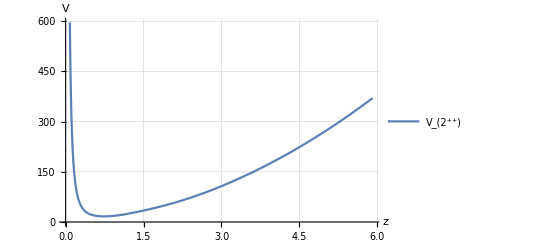

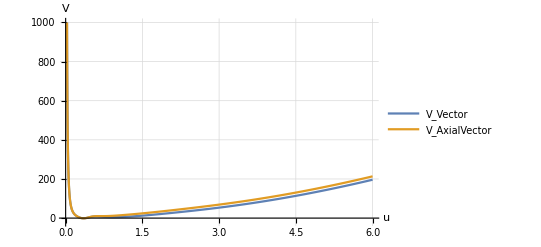

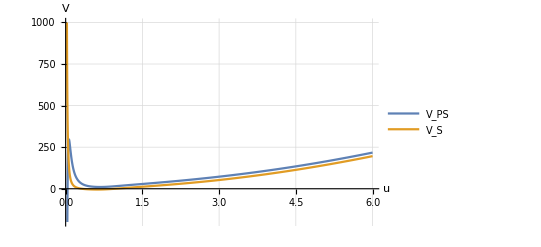

```mathematica
Plot[VTensorGlueballProfile[z],{z,zf[-40],zf[20]},AxesLabel->{"z","V"},PlotLegends->{"V_(2^(++))"},GridLines->Automatic]
Plot[{VVectorMesonProfile[u],VAxialVectorMesonProfile[u]},{u,0.001,6},AxesLabel->{"u","V"},PlotLegends->{"V_Vector","V_AxialVector"},PlotRange->{-20,1000},GridLines->Automatic]
Plot[{VPseudoScalarMesonProfile[u],VScalarMesonProfile[u]},{u,0.001,6},AxesLabel->{"u","V"},PlotLegends->{"V_PS","V_S"},GridLines->Automatic,PlotRange->{-200,1000}]
```

```mathematica
(* Solve the Schrodinger problem numerically *)
(* 2^(++) *)
schTensorGlueball=-ψ''[z]+VTensorGlueballProfile[z]ψ[z];
{valTensorGlueball,wfsTensorGlueball} =NDEigensystem[schTensorGlueball,ψ,{z,zf[-40],zf[20]},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
(* Vector Mesons *)
schVVectorMesons=-ψ''[u]+VVectorMesonProfile[u]ψ[u];
{valVVectorMesons,wfsVVectorMesons} =NDEigensystem[schVVectorMesons,ψ,{u,Re@uf[-40],Re@uf[20]},6,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
(* Axial Vector Mesons *)
schVAxialVectorMesons=-ψ''[u]+VAxialVectorMesonProfile[u]ψ[u];
{valVAxialVectorMesons,wfsVAxialVectorMesons} =NDEigensystem[schVAxialVectorMesons,ψ,{u,Re@uf[-40],Re@uf[20]},5,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
(* Pseudo-Scalar Mesons *)
schPseudoScalarMesons=-ψ''[u]+VPseudoScalarMesonProfile[u]ψ[u];
{valPseudoScalarMesons,wfsPseudoScalarMesons} =NDEigensystem[schPseudoScalarMesons,ψ,{u,Re@uf[-40],Re@uf[20]},5,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
(* Scalar Mesons *)
schScalarMesons=-ψ''[u]+VScalarMesonProfile[u]ψ[u];
{valScalarMesons,wfsScalarMesons} =NDEigensystem[schScalarMesons,ψ,{u,Re@uf[-40],Re@uf[20]},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

Compile::extscalar: NDSolve`FEM`FEMDiscretizationDump`temp cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

General::stop: Further output of Compile::extscalar will be suppressed during this calculation.

Compile::extscalar: NDSolve`FEM`FEMDiscretizationDump`temp cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

General::stop: Further output of Compile::extscalar will be suppressed during this calculation.

Compile::extscalar: NDSolve`FEM`FEMDiscretizationDump`temp cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

General::stop: Further output of Compile::extscalar will be suppressed during this calculation.

Compile::extscalar: NDSolve`FEM`FEMDiscretizationDump`temp cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

General::stop: Further output of Compile::extscalar will be suppressed during this calculation.

Compile::extscalar: NDSolve`FEM`FEMDiscretizationDump`temp cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

General::stop: Further output of Compile::extscalar will be suppressed during this calculation.

```mathematica
tensorGlueballMasses=Sqrt/@valTensorGlueball
vectorMesonMasses=Sqrt/@valVVectorMesons
axialVectorMesonMasses=Sqrt/@valVAxialVectorMesons
PseudoScalarMesonMasses=Sqrt/@valPseudoScalarMesons
ScalarMesonMasses = Sqrt/@valScalarMesons
```

{4.97438}

{3.07511,4.28006,5.31309,6.1943,6.94933,7.61651}

{3.70759,5.04957,6.11173,6.97464,7.70353}

{4.37768,5.75264,6.6926,7.46332,8.13444}

{1.57871,3.88693}

```mathematica
Print["Tensor Glueball Ratio:"]
tensorGlueballMasses/PseudoScalarMesonMasses[[1]]
Print["Vector Meson Ratio:"]
vectorMesonMasses/PseudoScalarMesonMasses[[1]]
Print["Axial Vector Meson Ratio:"]
axialVectorMesonMasses/PseudoScalarMesonMasses[[1]]
Print["Pseudo Scalar Meson Ratio:"]
PseudoScalarMesonMasses[[2;;]]/PseudoScalarMesonMasses[[1]]
Print["Scalar Meson Ratio:"]
ScalarMesonMasses/PseudoScalarMesonMasses[[1]]
```

Tensor Glueball Ratio:

{1.1363}

Vector Meson Ratio:

{0.702451,0.9777,1.21368,1.41497,1.58744,1.73985}

Axial Vector Meson Ratio:

{0.846929,1.15348,1.39611,1.59323,1.75973}

Pseudo Scalar Meson Ratio:

{1.31408,1.5288,1.70486,1.85816}

Scalar Meson Ratio:

{0.360628,0.887897}